## Initialization

```mathematica
$path="D:\\Documents\\aDependence\\";
```

```mathematica
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_4_energyVs2.mx"];
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_4_efV4.mx"];
Get["D:\\Documents\\DataDump_MultipleShortRangePotential_4_efVs2.mx"];
```

```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<a,Fa,0];
V4[r_,Ff_,Fg_]=-α/r+Ff E^(-Fg r);
V5[r_,Fi_,Fj_]=-α/r+Fi E^(-Fj r^2);
```

```mathematica
Fa=-2.71562984954227987707220753658717987150651086990482099679916347484158640580824`50.;
```

```mathematica
{Ff,Fg}={-4.20415644616125582469299138439140113373493210258692526366760104908016252690683`50.,1.88979567639491639010430213789778028047296373449456361136288297937037496900499`50.};
```

```mathematica
{Fi,Fj}={Fi,Fj}/.{Fi->-2.647828543053613773374298558957824633572173998851964865568`30.,Fj->1.0017713271893313754426035031926440089474493688810307925058`30.};
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
(*EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[evShifted[[n]],3],1.01 SetPrecision[evShifted[[n]],3]},opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]*)
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
Flatten@ParallelMap[EigenEnergySolo[V,αSch,{min,max},{SetPrecision[0.99#,3],SetPrecision[1.01#,3]},{opt1},{opt2}]&,evShifted]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
(*time1=SessionTime[];*)
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
(*time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
(*PrintTemporary[V];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)];
PrintTemporary[evnew];
evnew]
```

```mathematica
lap[f_,r_]:=Simplify[(2 D[f,r])/r+D[f,{r,2}]]
```

```mathematica
enV4=EigenEnergy[V4[r,Ff,Fg],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

{-1.3822,-0.182736,-0.0703652,-0.0371487,-0.0229267,-0.0155492,-0.0112354,-0.00849649,-0.00664955,-0.00534542,-0.00439048,-0.00367033,-0.00311387,-0.00267499,-0.00232276,-0.00203579,-0.00179889,-0.00160106,-0.00143415,-0.00129204}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$876]-u''[r$876]/2==e$875 u[r$876],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1598]-u''[r$1598]/2==e$1597 u[r$1598],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1970]-u''[r$1970]/2==e$1969 u[r$1970],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1898]-u''[r$1898]/2==e$1897 u[r$1898],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 5.3921284166692184286726269019×10^-12; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0112354034510922433745620596795}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2034]-u''[r$2034]/2==e$2033 u[r$2034],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 1.10593030659208195328348062432×10^-14; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

{-0.0371486908262772219712337835749}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1656]-u''[r$1656]/2==e$1655 u[r$1656],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00534541931000000385411444436383}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2034]-u''[r$2034]/2==e$2033 u[r$2034],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0229266892452571510305833713611}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1716]-u''[r$1716]/2==e$1715 u[r$1716],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00849649089104769793162473284283}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2154]-u''[r$2154]/2==e$2153 u[r$2154],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0043904785056545552104791995888}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2156]-u''[r$2156]/2==e$2155 u[r$2156],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.00664954945575757407656238553638}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2218]-u''[r$2218]/2==e$2217 u[r$2218],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 2.00475870223899641243219237754×10^-9; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0155492318552683040551357411273}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1778]-u''[r$1778]/2==e$1777 u[r$1778],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 2.33662312964044064156132728134×10^-8; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 2.00475870223899641243219237754×10^-9; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 2.33662312964044064156132728134×10^-8; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 2.00475870223899641243219237754×10^-9; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ParametricNDSolve::nderr: Error test failure at r == 2.33662312964044064156132728134×10^-8; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-0.0036703327576889355526415388256}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2264]-u''[r$2264]/2==e$2263 u[r$2264],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::nderr: Error test failure at r == 1.37885979753795258121406726736×10^-7; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 1.37885979753795258121406726736×10^-7; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 1.37885979753795258121406726736×10^-7; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00179888914720532927576372709818}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2338]-u''[r$2338]/2==e$2337 u[r$2338],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00232276446482712109250305199886}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$1890]-u''[r$1890]/2==e$1889 u[r$1890],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00311386894651937279668660448626}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2344]-u''[r$2344]/2==e$2343 u[r$2344],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00203578876875439127424041402994}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2016]-u''[r$2016]/2==e$2015 u[r$2016],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00160105779040613955997512218812}

ParametricNDSolve::nderr: Error test failure at r == 6.43339305598073024321950611184×10^-7; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00267499298242404204314245653497}

ParametricNDSolve::nderr: Error test failure at r == 6.43339305598073024321950611184×10^-7; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r == 6.43339305598073024321950611184×10^-7; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00143415343774481125324446617179}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$2116]-u''[r$2116]/2==e$2115 u[r$2116],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00129205009999999805332816239093}

{-1.38219883569252068764264326743}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$936]-u''[r$936]/2==e$935 u[r$936],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.182735548644293920169611977735}

ParametricNDSolve::precw: The precision of the differential equation ({{(-4.2041564461612558246929913843914011337349321025869 Power[«2»]-Power[«2»]) u[r$996]-u''[r$996]/2==e$995 u[r$996],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0703651929305042713156049691866}

{-1.38219883569252068764264326743,-0.182735548644293920169611977735,-0.0703651929305042713156049691866,-0.0371486908262772219712337835749,-0.0229266892452571510305833713611,-0.0155492318552683040551357411273,-0.0112354034510922433745620596795,-0.00849649089104769793162473284283,-0.00664954945575757407656238553638,-0.00534541931000000385411444436383,-0.0043904785056545552104791995888,-0.0036703327576889355526415388256,-0.00311386894651937279668660448626,-0.00267499298242404204314245653497,-0.00232276446482712109250305199886,-0.00203578876875439127424041402994,-0.00179888914720532927576372709818,-0.00160105779040613955997512218812,-0.00143415343774481125324446617179,-0.00129205009999999805332816239093}

```mathematica
Export[$path<>"enV4.dat",enV4,"CSV"];
```

```mathematica
enV4=Flatten@Import[$path<>"enV4.dat","CSV"];
```

```mathematica
AbsoluteTiming[efV4=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[PrintTemporary[n];
efunction[[n]]=First@Eigenfunsin[V4[r,Ff,Fg],enV4[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.01},{Exclusions->1}];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

```mathematica
lapV4=Table[lap[efV4[[n]]/(√(4π)r),r],{n,20}];
```

Calculation

### Determine c_1a

```mathematica
δexpminus10=δ50e[10^-10,V4[r,Ff,Fg]];
δexpminus9=δ50e[10^-9,V4[r,Ff,Fg]];
δexpminus5=δ50e[10^-5,V4[r,Ff,Fg]];
δ50V=δ50[V4[r,Ff,Fg]];
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031979700136220568923737045153765763046169357856) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631708196101944706820810514600259947125) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095933881080621951847950360718656142026828058) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.031974420815225174201553345413564726027527601002) is less than WorkingPrecision (50.).

{1/1000000,-0.031963530999942135580066285495419263636274009590628}    0.375003

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631708196101944706820810514600259947125) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.898866) is less than WorkingPrecision (50.).

{1/1000000000,-0.0010112864184230643500148805306756656692007495975031}    0.468756

{0.001,-0.7321881886441398085256379622073714870909292729968}    0.453129

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22646) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.003+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.01,-0.88676155322699035465597610067948784396837490388424}    0.531256

NDSolve::precw: The precision of the differential equation ({{2 (0.03+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10095933881080621951847950360718656142026828058) is less than WorkingPrecision (50.).

{1/100000,-0.10061840240122352411779974957434610910660152958619}    0.390629

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0031979647948935045155032628991570275865509771807) is less than WorkingPrecision (50.).

{1/100000000,-0.0031979538931209815977792456738464217491239704203567}    0.453129

FindRoot::precw: The precision of the argument function (Tan[δ]==10296.9) is less than WorkingPrecision (50.).

{0.003,1.5706992101715791374523098598121078917781790729407}    0.546883

NDSolve::precw: The precision of the differential equation ({{2 (0.007+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.20601) is less than WorkingPrecision (50.).

{0.03,-0.20316806883625407759244658829433575182079243420634}    0.671882

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.3137741414855291701290996588875885404116769049) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.07+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000,-0.30404523064061299584131420827842479776341551966039}    0.500006

NDSolve::precw: The precision of the differential equation ({{2 (0.3+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010112702576834871036503197245326290954321098893) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0165544) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1/10000000,-0.010112357866899140505986915285447471584998824147067}    0.546881

{0.007,0.01655287990685862097529993439524812391184369120353}    0.468753

FindRoot::precw: The precision of the argument function (Tan[δ]==0.811179) is less than WorkingPrecision (50.).

{0.07,0.68152055882262457337769553340136258946948049641742}    0.7187593

NDSolve::precw: The precision of the differential equation ({{2 (0.1+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.619716) is less than WorkingPrecision (50.).

{0.3,0.55479081458935396539221168434804941081019572710449}    0.9375086

NDSolve::precw: The precision of the differential equation ({{2 (0.7+4.2041564461612558246929913843914011337349321025869 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.147218) is less than WorkingPrecision (50.).

{0.1,-0.14616851862628250847675251201766201303321356306166}    0.8593827

FindRoot::precw: The precision of the argument function (Tan[δ]==12.9891789731678850814023216327706641141661936) is less than WorkingPrecision (50.).

{1,1.493960729710249209744116352257949168017977212268}    1.421893

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.75911) is less than WorkingPrecision (50.).

{0.7,-1.0538847911917323343668059082008077617705426516002}    1.203138

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.03593610455162919837654294256946783416409952901) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.3189157216471386286670039213653631845061256852) is less than WorkingPrecision (50.).

{3,-0.035920647188492847603768899283743717562244932101418}    2.203145

{7,-0.922068755563445059353059350473503793718920670425}    3.640662

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.767747195216944774159169303847381220238135991) is less than WorkingPrecision (50.).

{10,-1.2240862385461119346183684028990904677821318549192}    3.531287

```mathematica
nRange=20;
```

```mathematica
hhhc1[en_,a_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]];
evnhhhc1[c1_]:=N[hhhc1[10^-10,a,c1]-δexpminus10,8];
Determinec1[a_,{start_,end___},opt___]:=Module[{findroot},
Print[a];
findroot=FindRoot[hhhc1[10^-10,a,c1]==δexpminus10,{c1,start,end},opt];
Print[c1/.findroot];
c1/.findroot
]
```

```mathematica
c1a={};
```

```mathematica
Module[{table},
table=ParallelTable[Block[{c1,a},
a=10^loga;
c1=Determinec1[a,{0},{MaxIterations->If[a>10,200,100],PrecisionGoal->10,WorkingPrecision->50}];
{a,c1}],{loga,DeleteDuplicates[Join[Range[2,1,-0.02],Range[1,0,-0.02],Range[0,-1,-0.1],Range[-1,-3,-0.4]]]}];
c1a=DeleteDuplicates@Sort[c1a~Join~table]
]
```

100.

63.0957

39.8107

25.1189

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.001697979230839371255597111761846442876101896285) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870131827447159790285729474411013289881625) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825568615731125747527397203589864186214156) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.001697979230839371255597111761846442876101896285) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-1.49951×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156082226654886369679990199569147367450379916) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870131827447159790285729474411013289881625) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-2.37657×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0016979789639632308645647528601905605311581397931) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825568615731125747527397203589864186214156) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-9.46129×10^-12 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000691533870525243164726960710465842933993016136078) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007080825572758629025120772111693799303613160617) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156082226654886369679990199569147367450379916) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-3.76661×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000839156083757748849528015936859001896362469132464) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-6.1206570715631785794601038896940551772680001036425

95.4993

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

0.69185370845535027230451773584433120098226093451467

60.256

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.9379175501239290642422905199449335803877762661019

38.0189

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-5.3006042392612653974928486063127297944283923374058

91.2011

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-22.402655481436362292157519583246547389342851407403

23.9883

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-4.5161865014523923764275184032750013128390850273827

87.0964

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.2682389344415086979493653464661211251657560396173

36.3078

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-137.02007874777688606839375884967922543876485245429

57.544

-3.7655267074976005390545322408519455130285593754175

83.1764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-8.0620072464926809590334504914134490449636143869063

22.9087

-3.0468001270947235807150948323306638010829619023557

79.4328

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-10.341606321357707869190375086628064924247540298695

54.9541

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-2.6197397176250362500371740452389301219600359349479

34.6737

-2.3582291558040602642455205116365092154334659468882

75.8578

-1.6980781109038312705634245865110503363813298366429

72.4436

-25.032071464194659932845854357790152295531198496392

52.4807

-1.9900763978805519102851305899368681241040296230586

33.1131

-1.0646481407007299310508167584489366290384695500499

69.1831

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-79.623507668431027613036115254168696014505504234088

21.8776

-8.5328969724996805137297979948515138899303332162248

50.1187

-1.3769198120098839364503407600212455781315840780414

31.6228

-0.45627228226395955245058479935620128758786665520908

66.0693

0.12868928293960658147063464210439037888556991967508

15.8489

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000652910489955880113546166917628975402602190245665) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000652910489955880113546166917628975402602190245665) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-5.96967×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00065291049039470811409662598153906458706963875939) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-0.77796560559268432424208697788962622187785597982984

30.1995

-6.8648839235509090820125382394335715584168886721511

20.893

-22.299664451518503556209969842995654390540020051055

47.863

-0.1909496567533770561269010973414060241774815996751

28.8403

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-2.9132264757436130634708378847075015519415742376961

15.1356

-6.2854420223182582786163230216288454173042341818566

19.9526

-6.8755429836567732328581393605266316640877269023522

45.7088

0.38633087707685627036250517578288168701799408781961

27.5423

-6.0975732052945621810954129709509435587924272440486

43.6516

-5.7149160977438578064951930137517012138754493919393

19.0546

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-2.3507978494721283662514539441132346262179166005389

14.4544

-5.3502248469537184318529166340222122806247395620253

41.6869

-40.598786779886672714930005879428222741644284958996

26.3027

-5.15066864635583931997015320993468521978734622731

18.197

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-1.7851795585473399850832984889048047716218084973414

13.8038

-4.6311271766636188882433979913542625389247162663917

10.

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575489469291939497592549879868890656703718613) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575489469291939497592549879868890656703718613) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-9.46129×10^-11 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000848575490619253753998743047466437804865337191654) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-4.5903092303118233654153647516961890768094312574858

17.378

-23.10802716492246570258740980393565493646846055266

6.30957

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381524771803805621294508526919277259435239) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381524771803805621294508526919277259435239) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-1.49951×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0007058381526560559240814728520309971721314179699) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-1.2159676273114716810412337294901598472863365504624

13.1826

-4.0317387392382989013913759185083640325678742030095

16.5959

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-36.076772422909280328258567712103747139507723410338

9.54993

-0.6430302807319432466519096806969160555938062645733

12.5893

-3.4731851208336704652814116190086267998062289457248

3.98107

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146167682903229914061418522311799381625457) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146167682903229914061418522311799381625457) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-2.37657×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000621578146508317488428220163767037076939316116899) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-9.2093524886325690454260201448844335102300520875575

6.0256

-0.066457159117750338570443023361043675586253800037872

12.0226

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-13.243146520135152518986943815026647173409106439387

9.12011

0.51349118496184767233969714062360434803998031469353

11.4815

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-36.758540908447656667275011855364083540867586592629

5.7544

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-12.822903377771714258942438656772810791841619657493

8.70964

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-4.0784101912137682692370698643941737940252890752507

3.80189

-14.856734960019722363229985413272585283276114802952

10.9648

-12.395381975333374112775166173130384578073946309683

8.31764

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-8.2399890506248154278892908334779153657636866864481

5.49541

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-3.5331520733335341864354324775795414576485978328673

3.63078

-14.46290663463896061359032877711468614028401881606

10.4713

-11.960490336194728521429427015554564231941071631673

7.94328

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-2.9829809011285689435788781639449224812584958185463

3.46737

-63.321950875335037810447200201715489818301757239862

2.51189

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577889898683544697998544264129055361964091685) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577889898683544697998544264129055361964091685) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-3.76661×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.008577887967918849532975581523052115611852350512) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-7.7440712746822665345084157294887964435663017413364

5.24807

-11.518350554920363719315788462686207848973816913427

7.58578

-2.4275824285263069693131497636652113416881810289288

3.31131

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

1.5917833622804166737448474533313291723191497221973

2.39883

-7.2403477355326776910158218011504524739552412272164

5.01187

-11.069270539180324969586732716530000906000592939691

7.24436

-10.6136337690813648353217749640590061181234012716

6.91831

-1.8667110892562290128602449157422334038297639935427

3.16228

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-191.12344276848781453557094939984816325670200358983

2.29087

-6.7289775088923276927917441383742472170881743914733

4.7863

-10.151747531605735352542476819849445951807198618157

6.60693

-1.3003602628904393017873295933792484408644988986837

3.01995

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-39.192467834436666322281173227007840680454026771248

2.18776

-6.2104463194961386321841366078431559298982382773278

4.57088

-9.6837102860267463780541881923392347813138968104525

1.65959

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588257256615862746155046428433718260457783) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588257256615862746155046428433718260457783) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-5.70099×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000836887588665527541510154229912604182576454104279) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

-0.72887374338901986745071408560915276633280811605313

2.88403

-5.6854573269128409895085880266959164411445566324283

4.36516

-0.15295793204926452538442065464205017616555899699954

2.75423

-108.34713263405506573525584511695034003819166295925

2.0893

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-233.47409078407170638797884129104981909362927575139

1.58489

-5.1547578477374341998310654077167376598275678491468

4.16869

-39.281674596060182176098401067623920108118004690396

1.99526

0.42642384185530025562604951562918338168832986523298

2.63027

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-238.73929553315850554421747424860768278042597598586

1.51356

-4.6189596761322677412640230770231961402070376470852

1.09648

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

-39.275008534657284549475795853031232917896816217431

1.90546

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089367901094246503744926379405179725908289082) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089367901094246503744926379405179725908289082) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-8.6288×10^-10 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000761089368022156930929276732532001698633813955792) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

1.008263165081492384017577694297784557629567175295

0.199526

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971241520645525842660423816735852021610647) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1.×10^-10+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971241520645525842660423816735852021610647) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000-4.74188×10^-9 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000689587971259847355107659603072979101828654726458) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-244.24273138026707119125462904777988868408079847764

1.44544

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-48.360625319025627677158926680734600620642504864592

0.158489

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-297.11537250758976285436183157026096633861950437467

1.04713

-217.96489466057735240868024806583503847365707470018

1.8197

-126.30370383523287910060111516892054729621206016959

1.38038

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-54.960695174225640003171220228254902524880360904754

0.125893

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

-307.1715995829325978353108222848135821449237986904

1.

-223.17444809391929186664046798323057500625424785783

1.7378

-128.90221152491297896032591637270168104574509583443

1.31826

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-64.828370055450994035728743325038502497148495962152

0.1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 50. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-317.86523652568737633451444075087794694730883068449

0.794328

-78.720280223693417510179005762215133518097442918712

0.0398107

-131.77275776645205940177110340179410201581109232333

1.25893

-228.32110442335923931339937405398006618651436390185

-181.34046080045237897906230773129286777844335749176

0.630957

-201.84587619483423041996191886012651804304866837061

0.0158489

-134.92920347836960602925924905291052685791893168449

1.20226

-48.208759449127543246672144916074068347499779422356

0.501187

-560.82476817722149942947913561005697906154557428451

0.00630957

-138.37696772906639746864361970389077183089809874875

1.14815

-47.101004411040658137459838798294068877316718730449

0.398107

-287.70350907928164075313924188064087413553422971857

-44.576500721242549920882972154596488555122757446711

0.316228

-43.365126220251066125061321251111572585372456144204

0.251189

-44.564702994705419166339343350958729674784943725071

-2.9802777135181724235679645573782181600108717558136×10^-7

0.00251189

-2.98027771351817242356796455737821816001087175593×10^-7

0.001

-2.9802777135181724235679645573782181600108717559487×10^-7

{{0.001,-2.9802777135181724235679645573782181600108717559487×10^-7},{0.00251189,-2.98027771351817242356796455737821816001087175593×10^-7},{0.00630957,-2.9802777135181724235679645573782181600108717558136×10^-7},{0.0158489,-560.82476817722149942947913561005697906154557428451},{0.0398107,-201.84587619483423041996191886012651804304866837061},{0.1,-78.720280223693417510179005762215133518097442918712},{0.125893,-64.828370055450994035728743325038502497148495962152},{0.158489,-54.960695174225640003171220228254902524880360904754},{0.199526,-48.360625319025627677158926680734600620642504864592},{0.251189,-44.564702994705419166339343350958729674784943725071},{0.316228,-43.365126220251066125061321251111572585372456144204},{0.398107,-44.576500721242549920882972154596488555122757446711},{0.501187,-47.101004411040658137459838798294068877316718730449},{0.630957,-48.208759449127543246672144916074068347499779422356},{0.794328,-181.34046080045237897906230773129286777844335749176},{1.,-317.86523652568737633451444075087794694730883068449},{1.04713,-307.1715995829325978353108222848135821449237986904},{1.09648,-297.11537250758976285436183157026096633861950437467},{1.14815,-287.70350907928164075313924188064087413553422971857},{1.20226,-138.37696772906639746864361970389077183089809874875},{1.25893,-134.92920347836960602925924905291052685791893168449},{1.31826,-131.77275776645205940177110340179410201581109232333},{1.38038,-128.90221152491297896032591637270168104574509583443},{1.44544,-126.30370383523287910060111516892054729621206016959},{1.51356,-244.24273138026707119125462904777988868408079847764},{1.58489,-238.73929553315850554421747424860768278042597598586},{1.65959,-233.47409078407170638797884129104981909362927575139},{1.7378,-228.32110442335923931339937405398006618651436390185},{1.8197,-223.17444809391929186664046798323057500625424785783},{1.90546,-217.96489466057735240868024806583503847365707470018},{1.99526,-39.275008534657284549475795853031232917896816217431},{2.0893,-39.281674596060182176098401067623920108118004690396},{2.18776,-108.34713263405506573525584511695034003819166295925},{2.29087,-39.192467834436666322281173227007840680454026771248},{2.39883,-191.12344276848781453557094939984816325670200358983},{2.51189,1.5917833622804166737448474533313291723191497221973},{2.63027,1.008263165081492384017577694297784557629567175295},{2.75423,0.42642384185530025562604951562918338168832986523298},{2.88403,-0.15295793204926452538442065464205017616555899699954},{3.01995,-0.72887374338901986745071408560915276633280811605313},{3.16228,-1.3003602628904393017873295933792484408644988986837},{3.31131,-1.8667110892562290128602449157422334038297639935427},{3.46737,-2.4275824285263069693131497636652113416881810289288},{3.63078,-2.9829809011285689435788781639449224812584958185463},{3.80189,-3.5331520733335341864354324775795414576485978328673},{3.98107,-4.0784101912137682692370698643941737940252890752507},{4.16869,-4.6189596761322677412640230770231961402070376470852},{4.36516,-5.1547578477374341998310654077167376598275678491468},{4.57088,-5.6854573269128409895085880266959164411445566324283},{4.7863,-6.2104463194961386321841366078431559298982382773278},{5.01187,-6.7289775088923276927917441383742472170881743914733},{5.24807,-7.2403477355326776910158218011504524739552412272164},{5.49541,-7.7440712746822665345084157294887964435663017413364},{5.7544,-8.2399890506248154278892908334779153657636866864481},{6.0256,-36.758540908447656667275011855364083540867586592629},{6.30957,-9.2093524886325690454260201448844335102300520875575},{6.60693,-9.6837102860267463780541881923392347813138968104525},{6.91831,-10.151747531605735352542476819849445951807198618157},{7.24436,-10.6136337690813648353217749640590061181234012716},{7.58578,-11.069270539180324969586732716530000906000592939691},{7.94328,-11.518350554920363719315788462686207848973816913427},{8.31764,-11.960490336194728521429427015554564231941071631673},{8.70964,-12.395381975333374112775166173130384578073946309683},{9.12011,-12.822903377771714258942438656772810791841619657493},{9.54993,-13.243146520135152518986943815026647173409106439387},{10.,-36.076772422909280328258567712103747139507723410338},{10.4713,-63.321950875335037810447200201715489818301757239862},{10.9648,-14.46290663463896061359032877711468614028401881606},{11.4815,-14.856734960019722363229985413272585283276114802952},{12.0226,0.51349118496184767233969714062360434803998031469353},{12.5893,-0.066457159117750338570443023361043675586253800037872},{13.1826,-0.6430302807319432466519096806969160555938062645733},{13.8038,-1.2159676273114716810412337294901598472863365504624},{14.4544,-1.7851795585473399850832984889048047716218084973414},{15.1356,-2.3507978494721283662514539441132346262179166005389},{15.8489,-2.9132264757436130634708378847075015519415742376961},{16.5959,-3.4731851208336704652814116190086267998062289457248},{17.378,-4.0317387392382989013913759185083640325678742030095},{18.197,-4.5903092303118233654153647516961890768094312574858},{19.0546,-5.15066864635583931997015320993468521978734622731},{19.9526,-5.7149160977438578064951930137517012138754493919393},{20.893,-6.2854420223182582786163230216288454173042341818566},{21.8776,-6.8648839235509090820125382394335715584168886721511},{22.9087,-79.623507668431027613036115254168696014505504234088},{23.9883,-8.0620072464926809590334504914134490449636143869063},{25.1189,-22.402655481436362292157519583246547389342851407403},{26.3027,-23.10802716492246570258740980393565493646846055266},{27.5423,-40.598786779886672714930005879428222741644284958996},{28.8403,0.38633087707685627036250517578288168701799408781961},{30.1995,-0.1909496567533770561269010973414060241774815996751},{31.6228,-0.77796560559268432424208697788962622187785597982984},{33.1131,-1.3769198120098839364503407600212455781315840780414},{34.6737,-1.9900763978805519102851305899368681241040296230586},{36.3078,-2.6197397176250362500371740452389301219600359349479},{38.0189,-3.2682389344415086979493653464661211251657560396173},{39.8107,-3.9379175501239290642422905199449335803877762661019},{41.6869,-4.6311271766636188882433979913542625389247162663917},{43.6516,-5.3502248469537184318529166340222122806247395620253},{45.7088,-6.0975732052945621810954129709509435587924272440486},{47.863,-6.8755429836567732328581393605266316640877269023522},{50.1187,-22.299664451518503556209969842995654390540020051055},{52.4807,-8.5328969724996805137297979948515138899303332162248},{54.9541,-25.032071464194659932845854357790152295531198496392},{57.544,-10.341606321357707869190375086628064924247540298695},{60.256,-137.02007874777688606839375884967922543876485245429},{63.0957,0.69185370845535027230451773584433120098226093451467},{66.0693,0.12868928293960658147063464210439037888556991967508},{69.1831,-0.45627228226395955245058479935620128758786665520908},{72.4436,-1.0646481407007299310508167584489366290384695500499},{75.8578,-1.6980781109038312705634245865110503363813298366429},{79.4328,-2.3582291558040602642455205116365092154334659468882},{83.1764,-3.0468001270947235807150948323306638010829619023557},{87.0964,-3.7655267074976005390545322408519455130285593754175},{91.2011,-4.5161865014523923764275184032750013128390850273827},{95.4993,-5.3006042392612653974928486063127297944283923374058},{100.,-6.1206570715631785794601038896940551772680001036425}}

```mathematica
Export[$path<>"c1aV4.dat",c1a,"CSV"];
```

```mathematica
c1a=Import["D:\\Documents\\aDependence\\c1aV4.dat","CSV"];
```

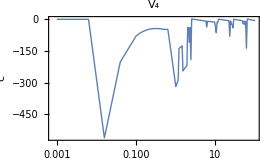

```mathematica
ListLogLinearPlot[c1a,ImageSize->270,Frame->True,Joined->True,PlotRange->All,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"c",None},{"a",None}},PlotStyle->Thick,PlotLabel->Style["V_4",15],RotateLabel->False,FrameTicksStyle->{{{Bold,11},{}},{{Bold,11},{}}}]
(*Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Plot_c1_veus_a.eps",%];*)
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=1;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{-36.2846073485848683455598356806,5.8412550011407563669641760073,0.000048354152,0.00015290929}

{-35.9154194490397907307718548026,5.78600358078768153868615504162,4.8342618×10^-6,0.000015287283}

{-36.3056922742570075203196473575,5.45531818058589715190060363081,4.1917196×10^-6,0.000013255385}

{-36.2637536276647644520882824144,5.45133647588196434660588203705,4.4320249×10^-8,1.4015361×10^-7}

{-36.2721675079924378564009062102,5.44394932728545553594203554005,-7.3516061×10^-11,-2.3184092×10^-10}

{-36.2721881053246393809424083681,5.44393227054383776791152700615,-7.3516032×10^-11,-2.3184083×10^-10}

{-36.2722079742857402338550709882,5.44391581697733108258361338319,-7.3515974×10^-11,-2.3184065×10^-10}

{-36.2721580418010362095104162377,5.44395785823272593002308193293,-1.8214719×10^-13,6.1342207×10^-14}

{-36.2721977586538120609820445116,5.44392496851604171273306195049,-1.8370578×10^-13,5.6405731×10^-14}

{-36.2721977586520138027564697499,5.44392496851753085717776775558,-1.8370578×10^-13,5.6405731×10^-14}

{-36.272197758652021581023366364,5.44392496851752441595698657684,-1.8370578×10^-13,5.6405731×10^-14}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-36.2721977586520215810233663642,5.44392496851752441595698657669}

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.59768,-0.180602,-0.0702185,-0.0371215,-0.0229188,-0.0155463,-0.0112341,-0.00849586,-0.00664921,-0.00534522,-0.00439036,-0.00367026,-0.00311382,-0.00267496,-0.00232274,-0.00203577,-0.00179888,-0.00160105,-0.00143415,-0.00129203}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$710]-u''[r$710]/2==e$709 u[r$710],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1106]-u''[r$1106]/2==e$1105 u[r$1106],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1218]-u''[r$1218]/2==e$1217 u[r$1218],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1216]-u''[r$1216]/2==e$1215 u[r$1216],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0112341240725214590649609599699}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1278]-u''[r$1278]/2==e$1277 u[r$1278],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.00534522265055337268285834080235}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1296]-u''[r$1296]/2==e$1295 u[r$1296],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.037121459914300833297457849076}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1162]-u''[r$1162]/2==e$1161 u[r$1162],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.00849585923549535096306976842572}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1340]-u''[r$1340]/2==e$1339 u[r$1340],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.00664920885965451537619023072179}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1404]-u''[r$1404]/2==e$1403 u[r$1404],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0229188406610151043984667510205}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1220]-u''[r$1220]/2==e$1219 u[r$1220],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00439035857161624206951038417806}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1448]-u''[r$1448]/2==e$1447 u[r$1448],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0155463160955231905919569956696}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1280]-u''[r$1280]/2==e$1279 u[r$1280],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00311381831204068409177633694448}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1544]-u''[r$1544]/2==e$1543 u[r$1544],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00367025626873854724290565582107}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1622]-u''[r$1622]/2==e$1621 u[r$1622],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00232274018200219398047220620639}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1442]-u''[r$1442]/2==e$1441 u[r$1442],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00267495838866846930601547026969}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1688]-u''[r$1688]/2==e$1687 u[r$1688],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00179887634763984600089029448282}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1750]-u''[r$1750]/2==e$1749 u[r$1750],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00203577131904286121925273747357}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00143414618079445478655792445233}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1834]-u''[r$1834]/2==e$1833 u[r$1834],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00160104823004255502766878811659}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0012920445114361318499644822901}

{-1.59768493239021475624777002261}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$766]-u''[r$766]/2==e$765 u[r$766],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.180602285051877852618818085632}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$822]-u''[r$822]/2==e$821 u[r$822],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0702185117971134206293124884613}

{{-1.59768493239021475624777002261},{-0.180602285051877852618818085632},{-0.0702185117971134206293124884613},{-0.037121459914300833297457849076},{-0.0229188406610151043984667510205},{-0.0155463160955231905919569956696},{-0.0112341240725214590649609599699},{-0.00849585923549535096306976842572},{-0.00664920885965451537619023072179},{-0.00534522265055337268285834080235},{-0.00439035857161624206951038417806},{-0.00367025626873854724290565582107},{-0.00311381831204068409177633694448},{-0.00267495838866846930601547026969},{-0.00232274018200219398047220620639},{-0.00203577131904286121925273747357},{-0.00179887634763984600089029448282},{-0.00160104823004255502766878811659},{-0.00143414618079445478655792445233},{-0.0012920445114361318499644822901}}

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V4.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V4.dat"];
```

```mathematica
Abs@((energyVs2-enV4)/enV4)
```

{0.1559009392376817065976715821,0.0116740481435749398257268089,0.0020845694764984068338302631,0.00073302480843084834026979965,0.0003423339566427049806190185,0.00018751792836155836960831,0.000113870283016844894779017,0.00007434310946093175096097205,0.00005122092937646957073150582,0.000036790275042271868904075,0.0000273168489855209034847705,0.000020839786318576690886854,0.0000162609536747855840175353,0.0000129322790003690921744857,0.000010454277777544420530234,8.57147450554592218980076×10^-6,7.11526082813923501863426×10^-6,5.9712795139687827881464×10^-6,5.0600934080513395087549×10^-6,4.3253461039965649165851×10^-6}

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.59768493239021475624777002261 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.037121459914300833297457849076 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112341240725214590649609599699 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534522265055337268285834080235 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439035857161624206951038417806 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229188406610151043984667510205 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849585923549535096306976842572 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.180602285051877852618818085632 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367025626873854724290565582107 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155463160955231905919569956696 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664920885965451537619023072179 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0702185117971134206293124884613 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311381831204068409177633694448 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232274018200219398047220620639 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179887634763984600089029448282 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143414618079445478655792445233 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267495838866846930601547026969 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203577131904286121925273747357 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160104823004255502766878811659 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0012920445114361318499644822901 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-1.97754199052×10^-470 ⅇ^(-r^2/2) r «1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (2.8699×10^-271 ⅇ^(-r^2/2) r «1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{0.011777620695565781618157277718,-0.000395709850941657806980480216138,-0.000228014646081190365718879219443,-0.000146454016141428273047909226384,-0.000103434947974172036579860814982,-0.000077850611626186254577769180507,-0.0000612599647704785380283602579235,-0.0000498040121809583867468729904554,-0.0000415110539895448019075403624268,-0.0000352835129776057773759714959063,-0.0000304681115662711169914856833994,-0.0000266546823635144846177117197356,-0.0000235742384515344043126626405896,-0.0000210438898537114251708141624573,-0.0000189354417946468974099214142553,-0.0000171566706930092561564692060909,-0.0000156397238467463779911047391805,-0.0000143336914446631532939590796884,-0.0000131997115790402234502843584509,-0.0000122076620042091485931380104625}

NIntegrate::precw: The precision of the argument function (5.03016177798×10^-1505 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) «1») is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function (-3.11455150019×10^-469 r«1»«1» InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},«25»,{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«20345»},{«1»}}}][r]) is less than WorkingPrecision (30.).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (30.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-0.0194412219859862542454853535559,-0.00707832358850823334841772319395,-0.00320936166211531119874828304771,-0.00193741943716303999522349618538,-0.00133383010081773238084916389418,-0.000990926051976820536487956017317,-0.000773891662246764625774045330113,-0.0006261802031051776425266944108,-0.000520246206829710578371393778558,-0.000441202543459358032330280104783,-0.000380361133203314810461998403551,-0.000332341946219514042232621213941,-0.000293652214187592161093982982158,-0.000261935133904028196856675142247,-0.000235548421314277503213208253248,-0.000213316090656634322157842506294,-0.000194376145904618336819679236601,-0.000178083800667630172633522772458,-0.000163948097570516063385418838739,-0.000151589292367875454947896064074}

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
ψrTrueVs2[20][-1,1]
```

-0.0017515212239834485173685798809

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV4[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV4[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrueVs2[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417946468974099214142553 γ-0.000235548421314277503213208253248 η)==0.0108279,4 π (-0.0000122076620042091485931380104625 γ-0.000151589292367875454947896064074 η)==0.00697422}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417946468974099214142553 γ-0.000235548421314277503213208253248 η)==0.010817,4 π (-0.0000122076620042091485931380104625 γ-0.000151589292367875454947896064074 η)==0.00696724}) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417946468974099214142553 γ-0.000235548421314277503213208253248 η)==0.0108062,4 π (-0.0000122076620042091485931380104625 γ-0.000151589292367875454947896064074 η)==0.00696024}) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V4.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V4.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

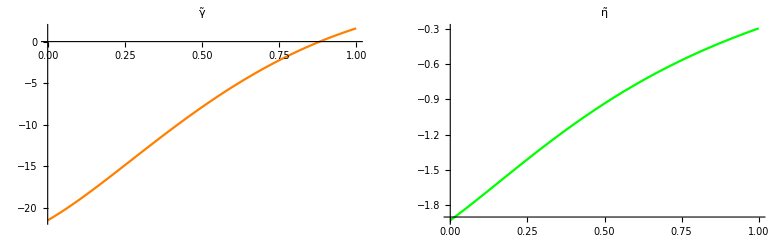

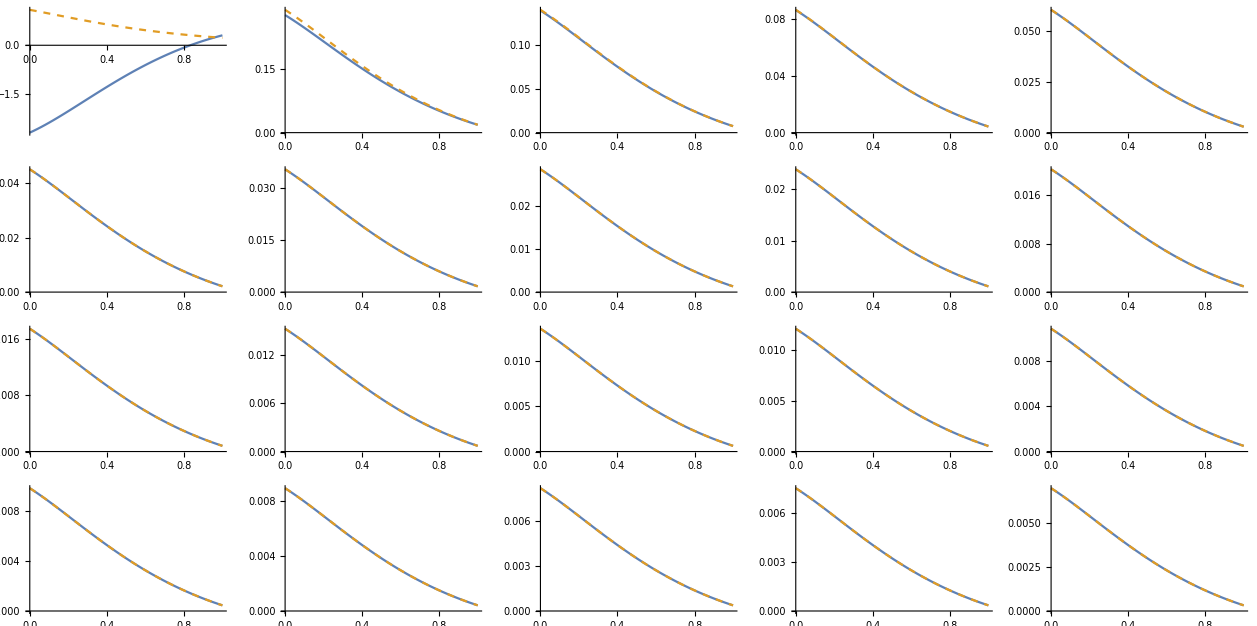

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV4[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV4[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

FindRoot::precw: The precision of the argument function ({4 π (-0.0000189354417946468974099214142553 γ-0.000235548421314277503213208253248 η)==-0.260175,4 π (-0.0000122076620042091485931380104625 γ-0.000151589292367875454947896064074 η)==-0.167591}) is less than WorkingPrecision (30.).

{{0.1,562.115330995567679933891639627},{0.1,42.7096676620944458474303135965}}

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

End

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V4.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V4.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

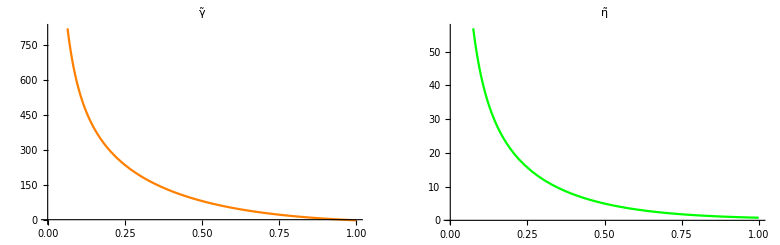

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

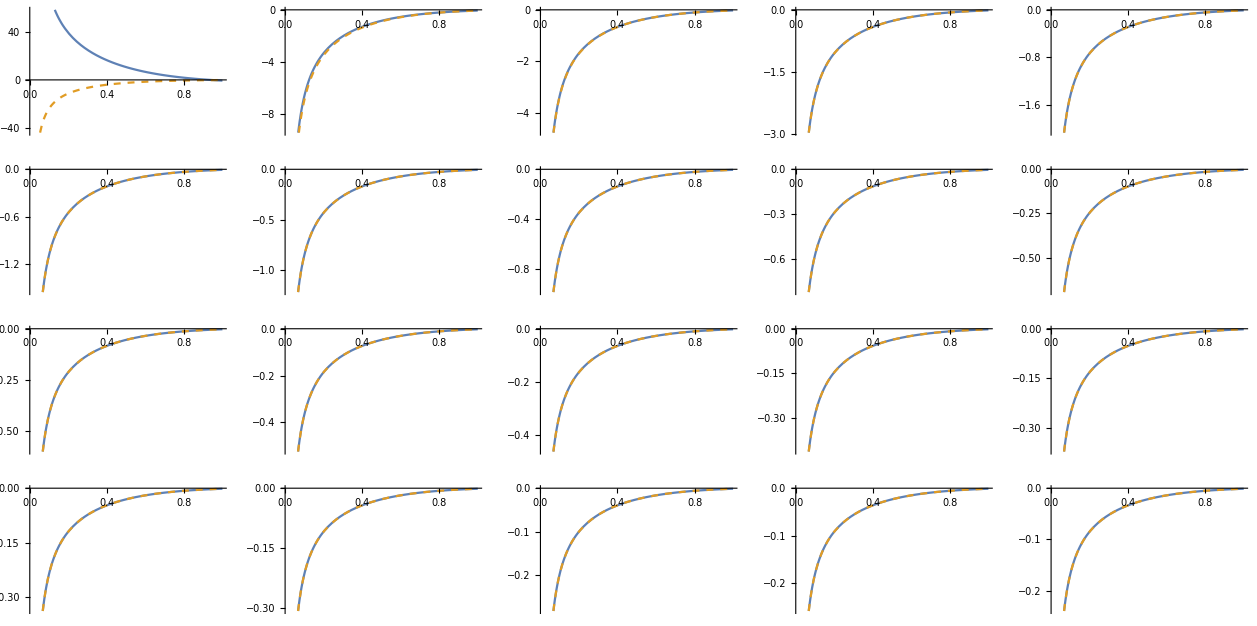

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV4[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.7;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031979700154591148948747383926679042456621936916) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010112867631144138211871644477582276278507432513) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.30305371902264276058167531414 Power[«2»]-5.44392496851752441595698657669 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00031979700154591148948747383926679042456621936916) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

{-39.9999999999999999999999999997,2.9999999999999999999999999999}

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.59768,-0.180602,-0.0702185,-0.0371215,-0.0229188,-0.0155463,-0.0112341,-0.00849586,-0.00664921,-0.00534522,-0.00439036,-0.00367026,-0.00311382,-0.00267496,-0.00232274,-0.00203577,-0.00179888,-0.00160105,-0.00143415,-0.00129203}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1490]-u''[r$1490]/2==e$1489 u[r$1490],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2670]-u''[r$2670]/2==e$2669 u[r$2670],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2892]-u''[r$2892]/2==e$2891 u[r$2892],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2888]-u''[r$2888]/2==e$2887 u[r$2888],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0112341240725214590649609599699}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2952]-u''[r$2952]/2==e$2951 u[r$2952],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.00534522265055337268285834080235}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2968]-u''[r$2968]/2==e$2967 u[r$2968],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.037121459914300833297457849076}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2726]-u''[r$2726]/2==e$2725 u[r$2726],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.00849585923549535096306976842572}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3014]-u''[r$3014]/2==e$3013 u[r$3014],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.00664920885965451537619023072179}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3078]-u''[r$3078]/2==e$3077 u[r$3078],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0229188406610151043984667510205}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2784]-u''[r$2784]/2==e$2783 u[r$2784],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00439035857161624206951038417806}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3120]-u''[r$3120]/2==e$3119 u[r$3120],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0155463160955231905919569956696}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$2844]-u''[r$2844]/2==e$2843 u[r$2844],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00311381831204068409177633694448}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3218]-u''[r$3218]/2==e$3217 u[r$3218],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00367025626873854724290565582107}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3294]-u''[r$3294]/2==e$3293 u[r$3294],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00232274018200219398047220620639}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3006]-u''[r$3006]/2==e$3005 u[r$3006],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00267495838866846930601547026969}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3362]-u''[r$3362]/2==e$3361 u[r$3362],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00179887634763984600089029448282}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3422]-u''[r$3422]/2==e$3421 u[r$3422],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00143414618079445478655792445233}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$3508]-u''[r$3508]/2==e$3507 u[r$3508],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00203577131904286121925273747357}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.00160104823004255502766878811659}

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

{-0.0012920445114361318499644822901}

{-1.59768493239021475624777002261}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1546]-u''[r$1546]/2==e$1545 u[r$1546],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.180602285051877852618818085632}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$1602]-u''[r$1602]/2==e$1601 u[r$1602],u[3000]==1.×10^-15,u'[3000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

{-0.0702185117971134206293124884613}

{-1.59768493239021475624777002261,-0.180602285051877852618818085632,-0.0702185117971134206293124884613,-0.037121459914300833297457849076,-0.0229188406610151043984667510205,-0.0155463160955231905919569956696,-0.0112341240725214590649609599699,-0.00849585923549535096306976842572,-0.00664920885965451537619023072179,-0.00534522265055337268285834080235,-0.00439035857161624206951038417806,-0.00367025626873854724290565582107,-0.00311381831204068409177633694448,-0.00267495838866846930601547026969,-0.00232274018200219398047220620639,-0.00203577131904286121925273747357,-0.00179887634763984600089029448282,-0.00160104823004255502766878811659,-0.00143414618079445478655792445233,-0.0012920445114361318499644822901}

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V4.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V4.dat"];
```

```mathematica
Abs@((energyVs2-enV4)/enV4)
```

{0.1559009392376817065976715821,0.0116740481435749398257268089,0.0020845694764984068338302631,0.00073302480843084834026979965,0.0003423339566427049806190185,0.00018751792836155836960831,0.000113870283016844894779017,0.00007434310946093175096097205,0.00005122092937646957073150582,0.000036790275042271868904075,0.0000273168489855209034847705,0.000020839786318576690886854,0.0000162609536747855840175353,0.0000129322790003690921744857,0.000010454277777544420530234,8.57147450554592218980076×10^-6,7.11526082813923501863426×10^-6,5.9712795139687827881464×10^-6,5.0600934080513395087549×10^-6,4.3253461039965649165851×10^-6}

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.59768493239021475624777002261 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.037121459914300833297457849076 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112341240725214590649609599699 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534522265055337268285834080235 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00439035857161624206951038417806 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229188406610151043984667510205 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849585923549535096306976842572 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.180602285051877852618818085632 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00367025626873854724290565582107 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155463160955231905919569956696 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664920885965451537619023072179 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0702185117971134206293124884613 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311381831204068409177633694448 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232274018200219398047220620639 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179887634763984600089029448282 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143414618079445478655792445233 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267495838866846930601547026969 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203577131904286121925273747357 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.30305371902264276058167531414 Power[«2»]+5.44392496851752441595698657669 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160104823004255502766878811659 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

$Aborted

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
ψrTrueVs2[20][-1,1]
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV4[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV4[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrueVs2[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V4.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V4.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV4[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV4[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V4.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V4.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV4[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.3;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V4.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V4.dat"];
```

```mathematica
Abs@((energyVs2-enV4)/enV4)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
ψrTrueVs2[20][-1,1]
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV4[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV4[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrueVs2[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V4.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V4.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV4[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV4[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V4.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V4.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV4[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
a=0.1;
```

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->100,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"c2d1V4.dat",energyVs2,"CSV"];
```

```mathematica
Import["D:\\Documents\\aDependence\\a=1c2d1V4.dat"];
```

```mathematica
Abs@((energyVs2-enV4)/enV4)
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},{WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.001},{}];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]];
```

#### ψ_r Vs_2

```mathematica
IntegrationVs21st=NIntegrate[efVs2[[#]]/(√(4π)r)δa[r] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
IntegrationVs22nd=NIntegrate[efVs2[[#]]/(√(4π)r)Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,2000},MaxRecursion->20,WorkingPrecision->30,AccuracyGoal->10]&/@Range@20
```

```mathematica
ψrTrueVs2[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
ψrTrueVs2[20][-1,1]
```

```mathematica
DetermineVs2[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV4[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
REF=NLimit[efV4[[#]]/(√(4π)r),r->r0]&/@REFRANGE;
RES=FindRoot[Thread[ψrTrueVs2[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTrueVs2[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}(*,N[ERROR,6]*)}/.RES
]
```

```mathematica
Module[{γη},
γlVs2={};ηlVs2={};
Monitor[Table[
γη=DetermineVs2[r0];
AppendTo[γlVs2,γη[[1]]];
AppendTo[ηlVs2,γη[[2]]];
,{r0,0,1,0.001}],Row[{ProgressIndicator[r0,{0,1}],100 r0/1"%"}]]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γlVs2V4.dat",γlVs2,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηlVs2V4.dat",ηlVs2,"CSV"];
```

```mathematica
γrVs2=Interpolation[γlVs2]
ηrVs2=Interpolation[ηlVs2]
```

```mathematica
ψrfunVs2[r_][n_]:=4π(γrVs2[r] IntegrationVs21st[[n]]+ηrVs2[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrVs2[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunVs2[r][n],efV4[[n]]/(√(4π)r)},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
ψrTruelap[n_][γ_,η_]:=4π(γ IntegrationVs21st[[n]]+η a^2 IntegrationVs22nd[[n]])
```

```mathematica
Determine[r0_]:=Module[{REAL,REF,RES,ψr,ERROR,Tru,REFRANGE={15,20}},
(*Print[r0];
REAL=NLimit[efV[[#]]/(√(4π)r),r->r0,WorkingPrecision->30]&/@Range@20;*)
Tru=lap[efV4[[#]]/(√(4π)r),r]&/@REFRANGE;
REF=Tru/.r->r0;
RES=FindRoot[Thread[ψrTruelap[#][γ,η]&/@REFRANGE==REF],{{γ,0,1},{η,0,1}},AccuracyGoal->10,MaxIterations->200,WorkingPrecision->30];
(*ψr=ψrTruelap[#][γ,η]/.RES&/@Range@20;
ERROR=Abs[(ψr-REAL)/REAL];
Print[N[ERROR,6]];*)
{{r0,γ},{r0,η}}/.RES
]
```

```mathematica
Determine[0.1]
```

```mathematica
Quiet@Module[{max=1,interval=0.01},
(*Zl=Determine[0][[1]];*)γllap={};ηllap={};
Monitor[Table[Module[{γη},
γη=Determine[r0];
(*AppendTo[Zl,γη[[1]]];*)
AppendTo[γllap,γη[[1]]];
AppendTo[ηllap,γη[[2]]];]
,{r0,0.01,max,interval}],Row[{ProgressIndicator[r0,{0,max}],100 r0/max"%"}]]
Print["End"]];
```

```mathematica
Export[$path<>"a="<>ToString[a]<>"γllapVs2V4.dat",γllap,"CSV"];
Export[$path<>"a="<>ToString[a]<>"ηllapVs2V4.dat",ηllap,"CSV"];
```

```mathematica
γrlap=Interpolation[γllap];
ηrlap=Interpolation[ηllap];
```

```mathematica
ψrfunlap[r_][n_]:=4π(γrlap[r] IntegrationVs21st[[n]]+ηrlap[r] a^2 IntegrationVs22nd[[n]])
```

```mathematica
GraphicsGrid@{{Plot[γrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Orange,PlotLabel->"γ̃"],Plot[ηrlap[r],{r,0,1},ImageSize->Medium,PlotStyle->Green,PlotLabel->"η̃"]}}
GraphicsGrid@Partition[Table[Plot[{ψrfunlap[r][n],lapV4[[n]]},{r,0,1},PlotStyle->{{},{Dashed}},ImageSize->230],{n,1,20}],5]
```

```mathematica
Exit;
FrontEndExecute[FrontEndToken["EvaluateInitialization"]];
```